```mathematica
f1[x_]:=Cos[x^2]/E^(0.2*x^2)+0.2*x
f2[x_]:=0.2*x
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
lstGrdLin={{-5,-3,3,5},{-1,-0.5,0.5,1}};
lstStyl1={{Blue,Thick},{Green,Thin,Dashed},{Red,Thin}};
lstStyl2={Directive[Thick,14],Directive[Thick,14]};
lstStyl3=Directive[Gray,Dotted];


rLgnd={"f1","f2","f3"};
Plot[{Sin[x^2],x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,3},ImageSize->540,PlotStyle->{{Blue,Thin},{Green,Thick,Dashed},{Red,Thick}},AxesStyle->{Directive[Black,Thick,14],Directive[Blue,Thick,22]},GridLines->{{1,1.5,2,2.5,3},{-6,-3,2,4}},GridLinesStyle->Directive[Gray,Dashed],PlotLabel->Style[Framed["Демонстрационный график с оформлением",FrameStyle->Red,RoundingRadius->5],16,Plain,Blue,Background->LightYellow],PlotLegends->Placed[SwatchLegend[rLgnd,LegendLabel->"Легенда (типы и вид линий):",LegendLayout->"Row",LegendFunction->"Frame"],{{0.2,-0.01},{0.3,-0.8}}]]
```

-Graphics-

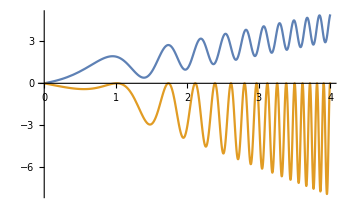
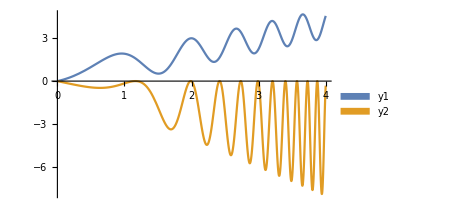

```mathematica
rLgnd={"y1","y2"};
pLgnd="Row";
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350];
grf2=Plot[{x+Sin[2*x^2],x*Sin[x^3]-x},{x,0,4},BaseStyle->18,ImageSize->350,PlotLegends->SwatchLegend[{y1,y2},LegendLayout->"Row"]];
Row[{grf1,grf2},Spacer[15]]
```

```mathematica
StringReplace["PlotLegends→SwatchLegend[{"y1","y2"},LegendLayout→"Row"]"," "]
```

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[] , },LegendLayout→ PlotLegends→SwatchLegend[{ Row y1 y2, ].

StringReplace[] , },LegendLayout→ PlotLegends→SwatchLegend[{ Row y1 y2, ]

```mathematica
StringLength[StringReplace[ToString["PlotLegends->SwatchLegend[{y1,y2},LegendLayout->"Row"]"],Whitespace..:>""]]
```

52

```mathematica
Clear[a,b,c,d,z,fRab];
fRab:=c*d+(d*z^4)/(c+d)+d*z^2/(b+z)-(d+z)/(b+c*z^2)+(z*(c+a*z^2))/(d+z^3);
fRab
Numerator[fRab[[4]]]//InputForm
```

c d+(d z^4)/(c+d)+(d z^2)/(b+z)-(d+z)/(b+c z^2)+(z (c+a z^2))/(d+z^3)

-d - z

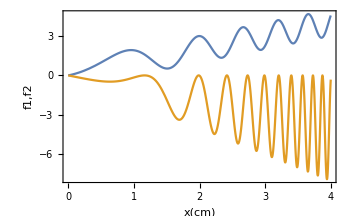
-Graphics--Graphics-

```mathematica
xFrmLbl="x(cm)";
yFrmLbl="f1,f2";
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350];
grf2=Plot[{x+Sin[2*x^2],x*Sin[x^3]-x},{x,0,4},BaseStyle->18,ImageSize->350,Frame->True,FrameLabel->{xFrmLbl,yFrmLbl}];
Row[{grf1,grf2},Spacer[15]]
```

```mathematica
lstR={1,4,73,9,-1,41,-7,-73,45,11,-2,40,3,-7,2,-5,11,5,41,8,42,73};
Select[lstR,x_/;Prime[x]&&x>10]
```

{}

```mathematica
bez = StringReplace[ToString["PlotLegends→SwatchLegend[{"y1","y2"},LegendLayout→"Row"]"],Whitespace..:>""]
StringLength[bez]
```

],},LegendLayout→PlotLegends→SwatchLegend[{Rowy1y2

50

```mathematica
"],},LegendLayout→PlotLegends→SwatchLegend[{Rowy1y2"
```

```mathematica
r=48828125;t=1/11;
#^t&[r]
p=40353607;q=1/9;
#^q&[p]
```

5

7

```mathematica
t = RandomInteger[12,{10,5}]//MatrixForm
Cases[t,{x_,___,___,x_,___}]
```

(0 | 5 | 11 | 7 | 6
0 | 7 | 10 | 8 | 9
5 | 3 | 0 | 11 | 2
11 | 8 | 8 | 8 | 5
12 | 6 | 1 | 2 | 3
10 | 3 | 11 | 10 | 6
9 | 2 | 10 | 1 | 9
6 | 12 | 4 | 4 | 7
0 | 12 | 8 | 6 | 4
11 | 12 | 7 | 7 | 11)

{}

```mathematica
CellEvaluationDuplicate
```

```mathematica
bez = StringReplace[ToString["PlotLegends→Placed[SwatchLegend[rLgnd,LegendLayout→"Row"],{Left,Bottom}]"],Whitespace..:>""]
StringLength[bez]
```

],{Left,Bottom}]PlotLegends→Placed[SwatchLegend[rLgnd,LegendLayout→Row

70

```mathematica
lstR={1,4,32,9,-1,41,-7,-73,38,11,-2,40,3,-7,2,-5,11,5,41,8,42,73};
```

```mathematica
Select[lstR, x_/;EvenQ[x]&&x<41]
```

Select::normal: Nonatomic expression expected at position 1 in Select[lstR,x_/;EvenQ[x]&&x<41].

Select[lstR,x_/;EvenQ[x]&&x<41]

```mathematica
f1[x_]:=Sin[1.5*x^3];
f2[x_]:=Cos[10*x^3];
grf1=Plot[x*f1[x]-x,{x,0.5,2.},PlotStyle->Purple];
grf2=Plot[x*f1[x]-x+0.5*f2[x],{x,0.5,2.},PlotStyle->Cyan];
grf3=Plot[x*f1[x]-x,{x,0.5,2.},PlotStyle->MeshShading];
grf4=Show[{grf1,grf2},PlotRange->{1,-5},BaseStyle->16,AxesOrigin->{0.5,-5},ImageSize->350];
grf5=Show[{grf2,grf3},PlotRange->{1,-5},BaseStyle->16,AxesOrigin->{0.5,-5},ImageSize->350];
Row[{grf4,grf5},Spacer[15]]
```

```mathematica
u=16777216;v=1/24;
#^v&[u]
```

2

```mathematica
FullSimplify[(35*(-((-(Sqrt[2]*3^(3/4))+2*Sqrt[3]*x)/(3-Sqrt[2]*3^(3/4)*x+Sqrt[3]*x^2))+(Sqrt[2]*3^(3/4)+2*Sqrt[3]*x)/(3+Sqrt[2]*3^(3/4)*x+Sqrt[3]*x^2)+(2*Sqrt[2])/(3^(1/4)*(1+(1-(Sqrt[2]*x)/3^(1/4))^2))+(2*Sqrt[2])/(3^(1/4)*(1+(1+(Sqrt[2]*x)/3^(1/4))^2))))/(28*Sqrt[2]*3^(3/4))]/.x->6/5//InputForm
```

3125/3171

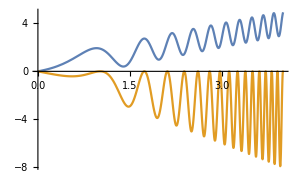
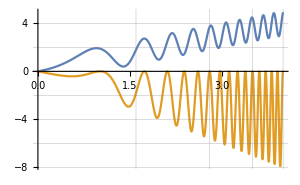

```mathematica
rClrTyp={Cyan,Dashed};
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},ImageSize->300];
grf2=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},ImageSize->300,GridLines->{{1.6,2.8,3.5,4}, {-8,-6,-4,-2,0,2,4}}];
Row[{grf1,grf2},Spacer[5]]
```

```mathematica
GridFrameMargins
```

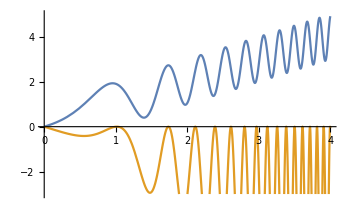
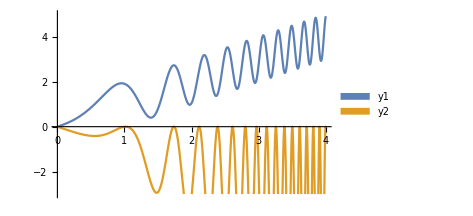

```mathematica
rLgnd={"y1","y2"};

grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350,PlotRange->{{0,4},{-3,5}}];
grf2=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350,PlotRange->{{0,4},{-3,5}},PlotLegends->Placed[SwatchLegend[rLgnd,LegendLayout->"Row"],{Left,Bottom}]];
Row[{grf1,grf2},Spacer[15]]
```